```mathematica
?Plot
```

PacletInstall::dwnld: An error occurred downloading paclet CloudObject-13.0.7 from site http://pacletserver.wolfram.com: Network error. Couldn't resolve host name

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", StyleBox["x", "TI"], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variable StyleBox["x", "TI"] to be in the geometric region StyleBox["reg", "TI"].



```mathematica
Plot[Sin[x], {x, 0, 2 Pi}]
```

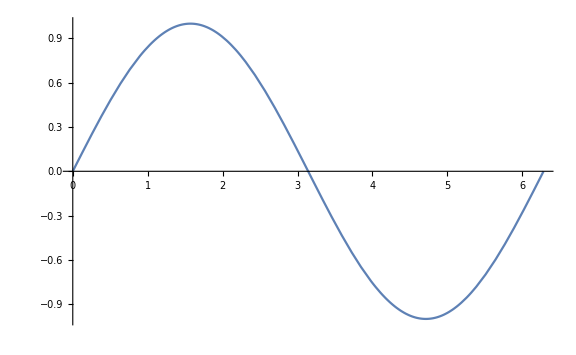

```mathematica
Plot[Sin[x], {x, 0, 2 Pi}, ImageSize -> Large]
```

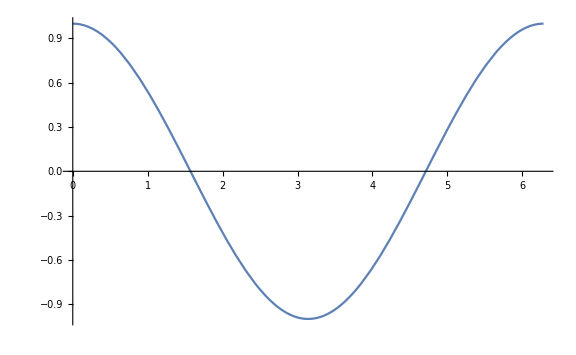

```mathematica
Plot[Cos[k], {k, 0, 2 Pi}, ImageSize -> Large]
```

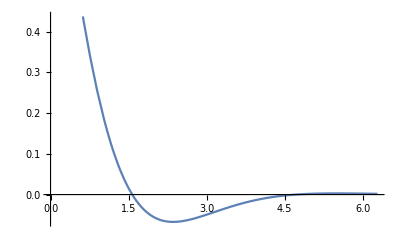

```mathematica
Plot[Exp[-x] * Cos[x], {x, 0, 2 Pi}]
```

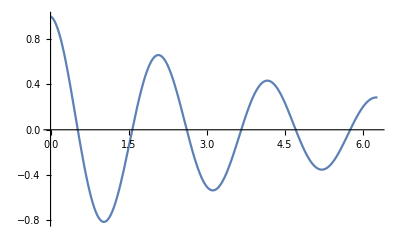

```mathematica
Plot[Exp[-0.2 x] * Cos[3 x], {x, 0, 2 Pi}]
```

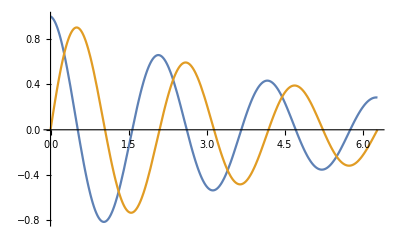

```mathematica
Plot[{Exp[-0.2 x] * Cos[3 x], Exp[-0.2 x] * Sin[3 x]}, {x, 0, 2 Pi}]
```

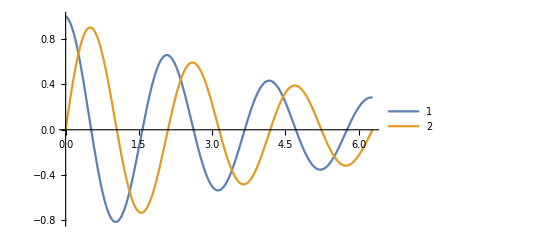

```mathematica
Plot[{Exp[-0.2 x] * Cos[3 x], Exp[-0.2 x] * Sin[3 x]}, {x, 0, 2 Pi}, PlotLegends-> Automatic]
```

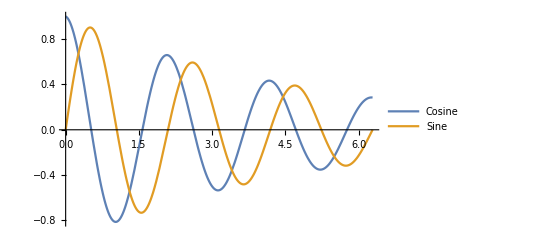

```mathematica
Plot[{Exp[-0.2 x] * Cos[3 x], Exp[-0.2 x] * Sin[3 x]}, {x, 0, 2 Pi}, PlotLegends-> {"Cosine", "Sine"}]
```

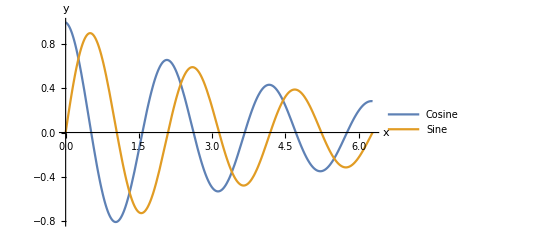

```mathematica
Plot[{Exp[-0.2 x] * Cos[3 x], Exp[-0.2 x] * Sin[3 x]}, {x, 0, 2 Pi}, PlotLegends-> {"Cosine", "Sine"}, AxesLabel -> {"x", "y"}]
```

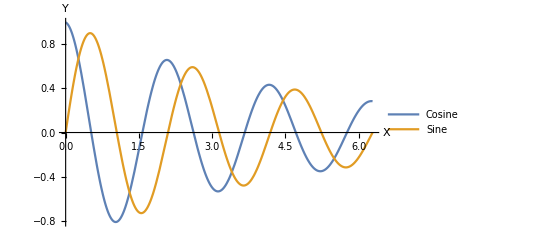

```mathematica
Plot[{Exp[-0.2 x] * Cos[3 x], Exp[-0.2 x] * Sin[3 x]}, {x, 0, 2 Pi}, PlotLegends-> {"Cosine", "Sine"}, AxesLabel -> {"X", "Y"}]
```

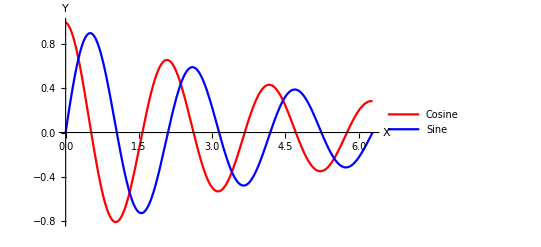

```mathematica
Plot[{Exp[-0.2 x] * Cos[3 x], Exp[-0.2 x] * Sin[3 x]}, {x, 0, 2 Pi}, PlotLegends-> {"Cosine", "Sine"}, AxesLabel -> {"X", "Y"}, PlotStyle -> {Red, Blue}]
```

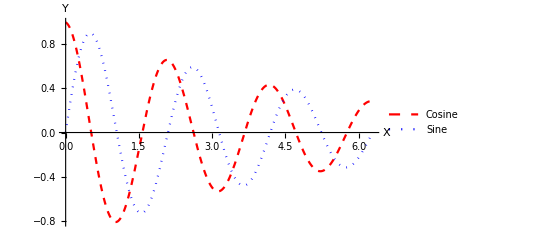

```mathematica
Plot[{Exp[-0.2 x] * Cos[3 x], Exp[-0.2 x] * Sin[3 x]}, {x, 0, 2 Pi}, PlotLegends-> {"Cosine", "Sine"}, AxesLabel -> {"X", "Y"}, PlotStyle -> {{Red, Dashed, Thick}, {Blue, Dotted}}]
```

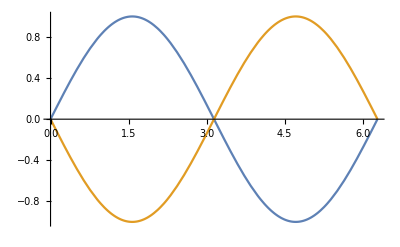

```mathematica
Plot[{Sin[x], Sin[x + Pi]}, {x, 0, 2 Pi}]
```

```mathematica
?{{GraphicsRow}, {□}}
```

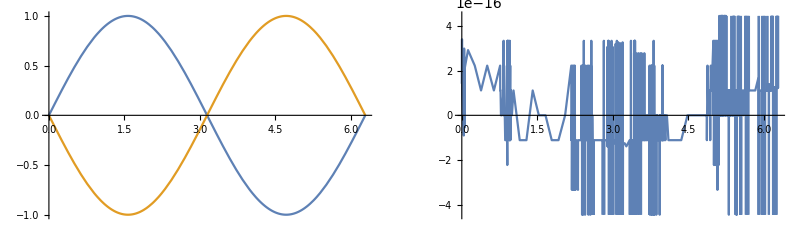

```mathematica
GraphicsRow[{Plot[{Sin[x], Sin[x + Pi]}, {x, 0, 2 Pi}], 
		      Plot[Sin[x] + Sin[x + Pi], {x, 0, 2 Pi}]}]
```

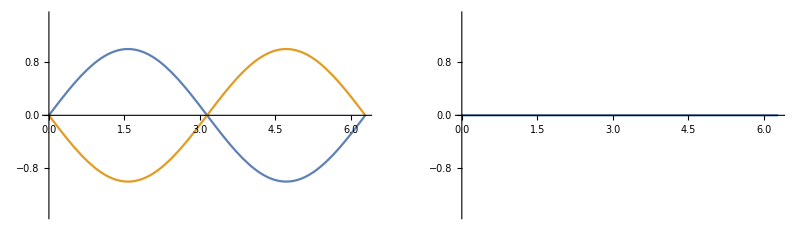

```mathematica
GraphicsRow[{Plot[{Sin[x], Sin[x + Pi]}, {x, 0, 2 Pi}, PlotRange -> {Automatic, {-1.5, 1.5}}], 
		      Plot[Sin[x] + Sin[x + Pi], {x, 0, 2 Pi}, PlotRange -> {Automatic, {-1.5, 1.5}}]}]
```